```mathematica
NSolve[Sin[Sqrt[x]]+Sqrt[x]Cos[Sqrt[x]]==0,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[√x Cos[√x]+Sin[√x]==0,x]

```mathematica
DSolve[{x''[t]+λ*x[t]==0, x[0]==0,x[1]+x'[1]==0},x[t],t]
```

{{x[t]→Piecewise[{{C[1] Sin[t √λ], √λ Cos[√λ]+Sin[√λ]==0}, {0, True}}]}}

```mathematica
x[t_]:=Piecewise[{{C[1] Sin[t √λ],√λ Cos[√λ]+Sin[√λ]==0}},0]
```

{{x[t]→0}}

```mathematica
NDSolve[{x''''[t]+λ*x[t]==0, x[0]==0,x'[0]==0, x'''[1]==0,x''''[1]==0},x[t],{t,0,1}]
```

NDSolve::icordinit: The initial values for all the dependent variables are not explicitly specified. NDSolve will attempt to find consistent initial conditions for all the variables.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{λ x[t]+x^(4)[t]==0,x[0]==0,x'[0]==0,x^(3)[1]==0,x^(4)[1]==0},x[t],{t,0,1}]

### 4. Visualizing Fourier Series

#### (1)

```mathematica
f41[x_,n_]:=∑_(k=1)^n 1/k Sin[k*Pi*x]
```

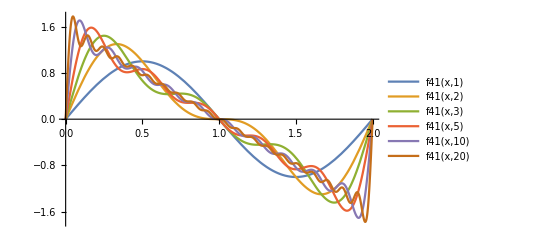

```mathematica
Plot[{f41[x,1],f41[x,2],f41[x,3],f41[x,5],f41[x,10],f41[x,20]},{x,0,2},PlotLegends->"Expressions"]
```

#### (2)

```mathematica
f42[x_,n_]:=∑_(k=1)^n (1/(Pi*k)+2/(Pi*k)^3(1-Cos[Pi*k]))Sin[k*Pi*x]
```

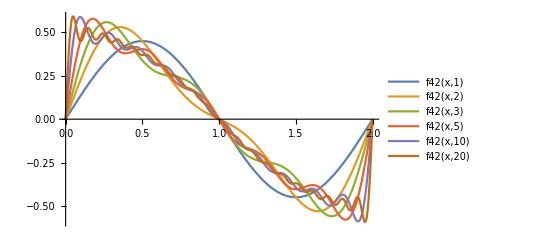

```mathematica
Plot[{f42[x,1],f42[x,2],f42[x,3],f42[x,5],f42[x,10],f42[x,20]},{x,0,2},PlotLegends->"Expressions"]
```

#### (3)

```mathematica
f43[x_,n_]:=∑_(k=1)^n ((-1)^k/(2k-1)^2)Cos[(2k-1)/2*Pi*x]
```

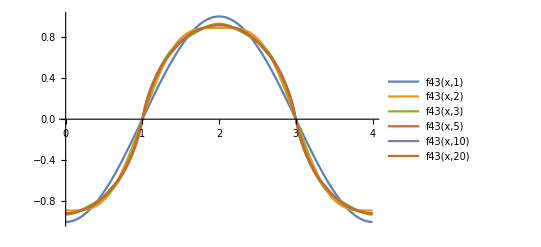

```mathematica
Plot[{f43[x,1],f43[x,2],f43[x,3],f43[x,5],f43[x,10],f43[x,20]},{x,0,4},PlotLegends->"Expressions"]
```

#### (4)

```mathematica
f44[x_,y_,n_]:=∑_(k=1)^n (-1)^k/k Sin[(2k-1)x]Sin[(2k-1)y]
```

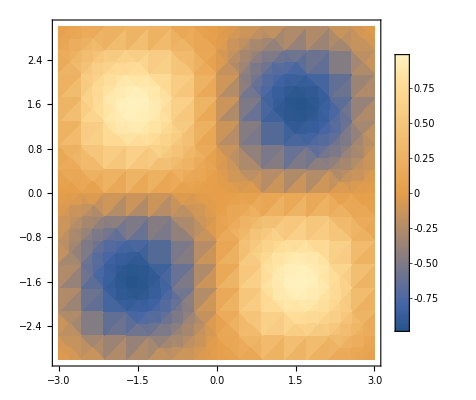

```mathematica
DensityPlot[f44[x,y,1],{x,-3,3},{y,-3,3},PlotLegends->Automatic]
```

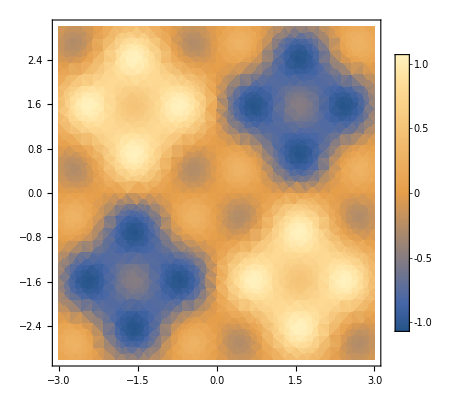

```mathematica
DensityPlot[f44[x,y,2],{x,-3,3},{y,-3,3},PlotLegends->Automatic]
```

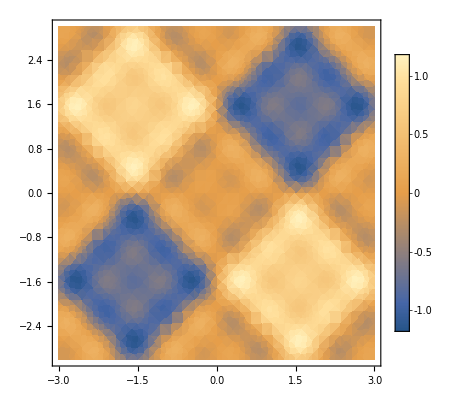

```mathematica
DensityPlot[f44[x,y,3],{x,-3,3},{y,-3,3},PlotLegends->Automatic]
```

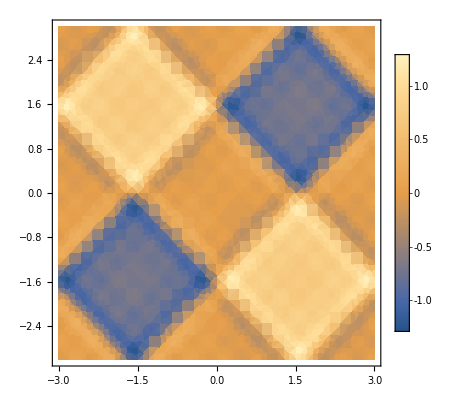

```mathematica
DensityPlot[f44[x,y,5],{x,-3,3},{y,-3,3},PlotLegends->Automatic]
```

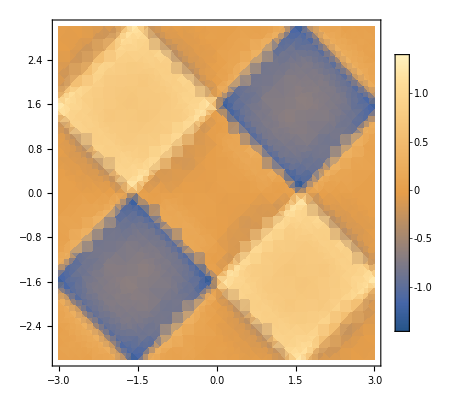

```mathematica
DensityPlot[f44[x,y,10],{x,-3,3},{y,-3,3},PlotLegends->Automatic,PerformanceGoal->"Quality"]
```

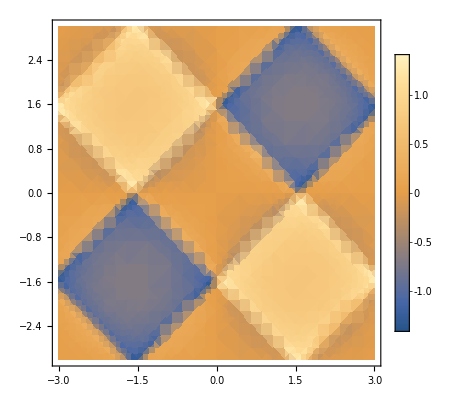

```mathematica
DensityPlot[f44[x,y,20],{x,-3,3},{y,-3,3},PlotLegends->Automatic]
```

```mathematica
Solve[0==2+2Cos[Sqrt[w]]Cosh[Sqrt[w]],w]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[0==2+2 Cos[√w] Cosh[√w],w]

```mathematica
Plot[2+2Cos[Sqrt[w]]Cosh[Sqrt[w]],{w,0,10000}]
```

-Graphics-

### Computing Fourier

```mathematica
Δ[x_]:=UnitTriangle[x]
```

```mathematica
$Assumptions={n∈Integers}
```

{n∈ℤ}

```mathematica
boxcar[x_]:=UnitStep[x]-UnitStep[x-1];
```

```mathematica
a1c[n_]:=(∫_-1^1 boxcar[x]Cos[(2*n*Pi*x)/2]ⅆx)/(∫_-1^1 (Cos[(2*n*Pi*x)/2])^2ⅆx)
```

```mathematica
a1c[0]
```

1/2

```mathematica
(∫_-1^1 boxcar[x]Sin[(2*n*Pi*x)/2]ⅆx)/(∫_-1^1 (Sin[(2*n*Pi*x)/2])^2ⅆx)
```

(1+(-1)^(1+n))/(n π)

#### (d)

```mathematica
(∫_-1^1 Δ[x]Sin[(2*n*Pi*x)/2]ⅆx)/(∫_-1^1 (Sin[(2*n*Pi*x)/2])^2ⅆx)
```

0

```mathematica
a1d[n_]:=FullSimplify[(∫_-1^1 Δ[x]Cos[(2*n*Pi*x)/2]ⅆx)/(∫_-1^1 (Cos[(2*n*Pi*x)/2])^2ⅆx)]
```

```mathematica
a1d[n]
```

-(2 (-1+(-1)^n))/(n^2 π^2)

#### (f)

```mathematica
FullSimplify[(∫_-1^1 Δ[x] Sin[5*Pi*x]*Sin[(2*n*Pi*x)/2]ⅆx)/(∫_-1^1 (Sin[(2*n*Pi*x)/2])^2ⅆx)]
```

(20 (1+(-1)^n) n)/((-25+n^2)^2 π^2)

```mathematica
a1g[n_]:=FullSimplify[(∫_-1^1 Δ[x] Sin[5*Pi*x]*Cos[(2*n Pi x)/2]ⅆx)/(∫_-1^1 (Cos[(2*n*Pi*x)/2])^2ⅆx)]
```

```mathematica
a1g[n]
```

0

```mathematica
FullSimplify[(∫_-1^1 (Δ[x] *Cos[(n Pi x)/2])^pⅆx)^(1/p)]
```

(∫_-1^1 (Cos[(n π x)/2] UnitTriangle[x])^p ⅆx)^(1/p)